```mathematica
f[x_]:=E^((1/2)(1-x)) (* outer approximation *)
```

```mathematica
g[x_] :=E^(1/2)(E^(-x/2) - E^(-2x/err)) (* exact approx, get it! *)
```

```mathematica
err=0.1
```

0.1

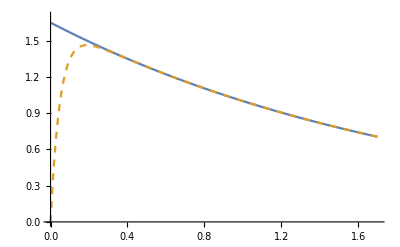

```mathematica
Plot[{f[x],g[x]}, {x, 0, 1.7},PlotRange -> {0,1.7},PlotStyle->{Dashing,Directive[Dashed],Directive[Thick]}]
```